```mathematica
0.03/(24*60)
```

0.0000208333

```mathematica
β=0.18;
γ=0.03;
t1 = 0;
t2 =100;
cmat = {
{1,1,0},
{1,1,1},
{0,1,1}
};

i0 = 1;
n = {2000+i0, 3000, 1500};
s[t_]:={s1[t] ,s2[t] ,s3[t] };
i[t_]:={i1[t] ,i2[t] ,i3[t] };
r[t_]:={r1[t] ,r2[t] ,r3[t] };
λ[a_,t_]:= β  Sum[ cmat[[a,b]] (i[t][[b]])/n[[b]],{b,1,3}]
```

```mathematica
sol = NDSolve[{
s'[t][[1]]== -λ[1,t] s[t][[1]],
s'[t][[2]]== -λ[2,t] s[t][[2]],
s'[t][[3]]== -λ[3,t] s[t][[3]],
i'[t][[1]]== λ[1,t] s[t][[1]] -γ i[t][[1]],
i'[t][[2]]== λ[2,t] s[t][[2]] -γ i[t][[2]],
i'[t][[3]]== λ[3,t] s[t][[3]] -γ i[t][[3]],
r'[t][[1]]== γ i[t][[1]],
r'[t][[2]]== γ i[t][[2]],
r'[t][[3]]== γ i[t][[3]],
s[0][[1]]== n[[1]],
s[0][[2]]== n[[2]],
s[0][[3]]== n[[3]],
i[0][[1]]==i0,
i[0][[2]]== 0,
i[0][[3]]==0,
r[0][[1]]== 0,
r[0][[2]]== 0,
r[0][[3]]==0
},Join[s[t],r[t],i[t]],{t,t1,t2}]
```

{{s1[t]→InterpolatingFunction[…][t],s2[t]→InterpolatingFunction[…][t],s3[t]→InterpolatingFunction[…][t],r1[t]→InterpolatingFunction[…][t],r2[t]→InterpolatingFunction[…][t],r3[t]→InterpolatingFunction[…][t],i1[t]→InterpolatingFunction[…][t],i2[t]→InterpolatingFunction[…][t],i3[t]→InterpolatingFunction[…][t]}}

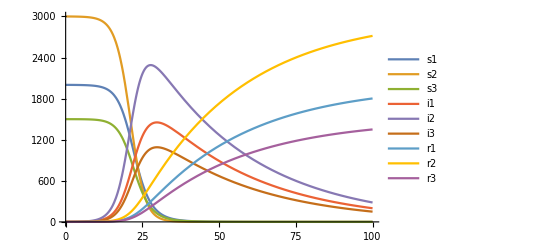

```mathematica
sols = Join[s[t],i[t],r[t]]/.sol//Flatten;
Plot[sols, {t,t1,t2},
PlotLegends->{"s1", "s2", "s3", "i1", "i2", "i3", "r1", "r2", "r3"}]
```

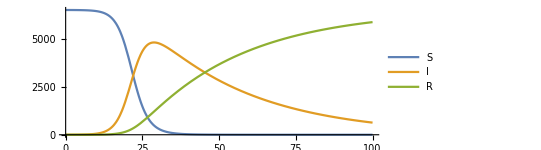

```mathematica
Plot[{
Total[s[t]/.sol//Flatten],
Total[i[t]/.sol//Flatten],
Total[r[t]/.sol//Flatten]
},{t,t1,t2},PlotLegends-> {"S","I","R"},AspectRatio->3/8]
```

```mathematica
ts = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.,30.,31.,32.,33.,34.,35.,36.,37.,38.,39.,40.,41.,42.,43.,44.,45.,46.,47.,48.,49.,50.,51.,52.,53.,54.,55.,56.,57.,58.,59.,60.,61.,62.,63.,64.,65.,66.,67.,68.,69.,70.,71.,72.,73.,74.,75.,76.,77.,78.,79.,80.,81.,82.,83.,84.,85.,86.,87.,88.,89.,90.,91.,92.,93.,94.,95.,96.,97.,98.,99.,100.};
ss={6500.0,6499.550224887556,6498.927830399,6498.072289083602,6496.902618386198,6495.310600986091,6493.15179704794,6490.233650277365,6486.299784058638,6481.009329558345,6473.9098227664135,6464.4018602061615,6451.693342206648,6434.740826184272,6412.175399354554,6382.210822252536,6342.532953920036,6290.172418490689,6221.368316000066,6131.44123097818,6014.710926838041,5864.51962089305,5673.454870857712,5433.899449307674,5139.048276806828,4784.483647785855,4370.232569675681,3902.905640405401,3397.098865547982,2874.988856791436,2363.383845684737,1888.6175035138372,1471.0774124832487,1121.6888662484284,841.6404281233241,624.8063025217208,461.188656406736,339.87681080235285,250.88201059335415,185.92874281892784,138.56954650915793,103.97026544067096,78.59031929258931,59.871262436824026,45.97676328396538,35.59163762472584,27.7730570242964,21.84306403073058,17.3119840755541,13.824226188756214,11.120020229147329,9.00839022180506,7.3480161211026545,6.033629287895567,4.986295698154091,4.146438857331053,3.468801346403843,2.9187847683236403,2.4697749391753256,2.101175232564641,1.796951838878217,1.5445512369015413,1.3340898818624711,1.1577441362191367,1.0092883473570193,0.8837431518346015,0.7771062494603305,0.6861452173956542,0.6082372451572348,0.5412445414777532,0.4834169993383417,0.4333157937088383,0.3897531324689396,0.35174453128119837,0.31847084336563436,0.28924792149647066,0.26350227756755346,0.24075147526426455,0.22058827346782353,0.2026677539278272,0.18669683271453114,0.17242568309365633,0.15964069679205434,0.1481586879295672,0.13782210429934028,0.12849505806194933,0.12006002522561622,0.11241509276598645,0.105471655619405,0.09915248439063053,0.09339009947457155,0.08812539919655399,0.08330649914503567,0.07888774758720177,0.07482888809958901,0.07109434560997913,0.06765261616762752,0.06447574412186403,0.06153887314135999,0.05881985976503877,0.056298940034244765};
ii = {1.0,1.419775112443778,1.999576347626465,2.7951303725952044,3.8809471588224076,5.356536144163655,7.3546439979900455,10.05215144862633,13.684453123895171,18.564374030471097,25.10694960148763,33.86170367369512,45.55437056299798,61.14025546848366,81.87147463414705,109.3799074971416,145.77637860472692,193.76362267593308,256.7548164862762,338.9792570135745,445.54018344330586,582.3652838849987,755.9590754037866,972.83572469171,1238.5018254518054,1555.911399709224,1923.4851358281217,2333.1075110235574,2768.9210605502694,3207.963437490308,3623.3295454722975,3989.3960012790285,4287.254212271247,4508.025132137929,4652.8328162988955,4730.081957411532,4751.797144804171,4730.555076064429,4677.633223991494,4602.257495046176,4511.548966504561,4410.80177857791,4303.857671368654,4193.46099808336,4081.5516672937183,3969.4902429341464,3858.2241162465516,3748.407385752721,3640.4862441353157,3534.7594146980537,3431.420838216721,3330.5898430775624,3232.3325218859372,3136.6769330625666,3043.6239586604306,2953.1550967414414,2865.238081350125,2779.8309554877014,2696.8850366522192,2616.3470852592627,2538.1608960951717,2462.2684698142934,2388.610877074904,2317.1288965082995,2247.763485401913,2180.456126035378,2115.1490791566907,2051.785567814055,1990.3099087518717,1930.667604192995,1872.8054036093445,1816.6713427066938,1762.2147650867328,1709.3863307353186,1658.1380145011744,1608.4230969880084,1560.1961497222972,1513.4130160329316,1468.0307887537401,1424.0077856106677,1381.3035229635611,1339.8786884242752,1299.6951127578486,1260.7157413839755,1222.9046057260864,1186.226794600541,1150.6484257953612,1116.13661795396,1082.6594628524876,1050.185998138142,1018.6861805789138,988.1308598618243,958.4917529660211,929.7414191285983,901.8532354142279,874.8013728942907,848.5607734369044,823.1071271058429,798.4168501636482,774.467063672115,751.2355726816825};
rr = {0.0,0.03,0.07259325337331334,0.13258054380210726,0.21643445497996341,0.33286286974463564,0.4935589540695453,0.7141982740092466,1.0157628174680364,1.4262964111848915,1.9832276320990243,2.736436120143653,3.752287230354507,5.118918347244446,6.953126011298957,9.409270250323367,12.690667475237616,17.063958833379424,22.876867513657416,30.579512008245704,40.74888971865294,54.11509522195211,71.58605373850207,94.26482600061567,123.44989774136697,160.60495250492113,207.28229449619784,264.9868485710415,334.9800739017482,418.04770571825634,514.2866088429656,622.9864952071345,742.6683752455053,871.2860016136426,1006.5267555777806,1146.1117400667474,1288.0141987890934,1430.5681131332185,1572.4847654151513,1712.8137621348965,1850.8814869862815,1986.2279559814183,2118.552009338756,2247.6677394798153,2373.471569422316,2495.9181194411276,2615.002826729152,2730.7495502165484,2843.2017717891304,2952.416359113189,3058.4591415541317,3161.401766700633,3261.3194619929595,3358.2894376495383,3452.389745641415,3543.698464401228,3632.2931173034713,3718.2502597439748,3801.6451884086055,3882.5517395081724,3961.0421520659506,4037.1869789488055,4111.055033043234,4182.713359355481,4252.22722625073,4319.660130812787,4385.0738145938485,4448.52828696855,4510.081854002971,4569.791151265528,4627.711179391317,4683.8953414995985,4738.395481780799,4791.261924733401,4842.543514655461,4892.287655090496,4940.540348000136,4987.3462324918055,5032.748622972793,5076.789546635405,5119.509780203725,5160.9488858926325,5201.145246545359,5240.136099928095,5277.957572169615,5314.6447103413975,5350.231514179413,5384.750966953274,5418.235065491893,5450.7148493774675,5482.220429321612,5512.78101473898,5542.424940534835,5571.179693123815,5599.071935697673,5626.1275327601,5652.371573946928,5677.828397150035,5702.52161096321,5726.47411646812,5749.708128378284};
```

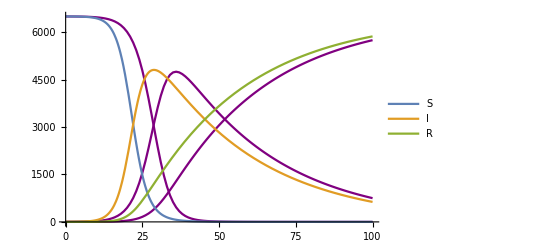

```mathematica
mt = 0;
Show[{
ListPlot[ {ts+mt, ss}//Transpose,Joined->True, PlotStyle->Purple],
ListPlot[ {ts+mt, ii}//Transpose,Joined->True, PlotStyle->Purple],
ListPlot[ {ts+mt, rr}//Transpose,Joined->True, PlotStyle->Purple],
Plot[{
Total[s[t]/.sol//Flatten],
Total[i[t]/.sol//Flatten],
Total[r[t]/.sol//Flatten]
},{t,t1,t2},PlotLegends-> {"S","I","R"},AspectRatio->3/8]}]
```

```mathematica
Total[i[t]/.sol//Flatten]/.t-> 30
```

4780.07

```mathematica
x=Table[sols[[1]],{t,t1,t2,1/60}]
```

{2001.,2001.,2000.99,2000.99,2000.99,2000.98,2000.98,2000.98,2000.98,2000.97,2000.97,2000.97,2000.96,2000.96,2000.96,2000.95,2000.95,2000.95,2000.94,2000.94,2000.94,2000.93,2000.93,2000.93,2000.92,2000.92,2000.92,2000.91,2000.91,2000.91,2000.9,2000.9,2000.9,2000.89,2000.89,2000.88,2000.88,2000.88,2000.87,2000.87,2000.87,2000.86,2000.86,2000.85,2000.85,2000.85,2000.84,2000.84,2000.84,2000.83,2000.83,2000.82,2000.82,2000.82,2000.81,2000.81,2000.8,2000.8,2000.8,2000.79,2000.79,2000.78,2000.78,2000.77,2000.77,2000.77,2000.76,2000.76,2000.75,2000.75,2000.74,2000.74,2000.73,2000.73,2000.73,2000.72,2000.72,2000.71,2000.71,2000.7,2000.7,2000.69,2000.69,2000.68,2000.68,2000.67,2000.67,2000.67,2000.66,2000.66,2000.65,2000.65,2000.64,2000.64,2000.63,2000.63,2000.62,2000.62,2000.61,2000.6,2000.6,2000.59,2000.59,2000.58,2000.58,2000.57,2000.57,2000.56,2000.56,2000.55,2000.55,2000.54,2000.53,2000.53,2000.52,2000.52,2000.51,2000.51,2000.5,2000.5,2000.49,2000.48,2000.48,2000.47,2000.47,2000.46,2000.45,2000.45,2000.44,2000.44,2000.43,2000.42,2000.42,2000.41,2000.4,2000.4,2000.39,2000.39,2000.38,2000.37,2000.37,2000.36,2000.35,2000.35,2000.34,2000.33,2000.33,2000.32,2000.31,2000.31,2000.3,2000.29,2000.28,2000.28,2000.27,2000.26,2000.26,2000.25,2000.24,2000.23,2000.23,2000.22,2000.21,2000.21,2000.2,2000.19,2000.18,2000.17,2000.17,2000.16,2000.15,2000.14,2000.14,2000.13,2000.12,2000.11,2000.1,2000.1,2000.09,2000.08,2000.07,2000.06,2000.06,2000.05,2000.04,2000.03,2000.02,2000.01,2000.,2000.,1999.99,1999.98,1999.97,1999.96,1999.95,1999.94,1999.93,1999.93,1999.92,1999.91,1999.9,1999.89,1999.88,1999.87,1999.86,1999.85,1999.84,1999.83,1999.82,1999.81,1999.8,1999.79,1999.78,1999.77,1999.76,1999.75,1999.74,1999.73,1999.72,1999.71,1999.7,1999.69,1999.68,1999.67,1999.66,1999.65,1999.64,1999.63,1999.62,1999.61,1999.6,1999.58,1999.57,1999.56,1999.55,1999.54,1999.53,1999.52,1999.51,1999.49,1999.48,1999.47,1999.46,1999.45,1999.44,1999.42,1999.41,1999.4,1999.39,1999.37,1999.36,1999.35,1999.34,1999.33,1999.31,1999.3,1999.29,1999.27,1999.26,1999.25,1999.24,1999.22,1999.21,1999.2,1999.18,1999.17,1999.16,1999.14,1999.13,1999.11,1999.1,1999.09,1999.07,1999.06,1999.04,1999.03,1999.02,1999.,1998.99,1998.97,1998.96,1998.94,1998.93,1998.91,1998.9,1998.88,1998.87,1998.85,1998.84,1998.82,1998.8,1998.79,1998.77,1998.76,1998.74,1998.73,1998.71,1998.69,1998.68,1998.66,1998.64,1998.63,1998.61,1998.59,1998.58,1998.56,1998.54,1998.52,1998.51,1998.49,1998.47,1998.45,1998.44,1998.42,1998.4,1998.38,1998.36,1998.35,1998.33,1998.31,1998.29,1998.27,1998.25,1998.23,1998.21,1998.19,1998.17,1998.16,1998.14,1998.12,1998.1,1998.08,1998.06,1998.04,1998.01,1997.99,1997.97,1997.95,1997.93,1997.91,1997.89,1997.87,1997.85,1997.83,1997.8,1997.78,1997.76,1997.74,1997.72,1997.69,1997.67,1997.65,1997.63,1997.6,1997.58,1997.56,1997.53,1997.51,1997.49,1997.46,1997.44,1997.41,1997.39,1997.37,1997.34,1997.32,1997.29,1997.27,1997.24,1997.22,1997.19,1997.17,1997.14,1997.11,1997.09,1997.06,1997.04,1997.01,1996.98,1996.96,1996.93,1996.9,1996.87,1996.85,1996.82,1996.79,1996.76,1996.74,1996.71,1996.68,1996.65,1996.62,1996.59,1996.56,1996.53,1996.5,1996.47,1996.44,1996.41,1996.38,1996.35,1996.32,1996.29,1996.26,1996.23,1996.2,1996.17,1996.13,1996.1,1996.07,1996.04,1996.,1995.97,1995.94,1995.9,1995.87,1995.84,1995.8,1995.77,1995.73,1995.7,1995.67,1995.63,1995.59,1995.56,1995.52,1995.49,1995.45,1995.42,1995.38,1995.34,1995.3,1995.27,1995.23,1995.19,1995.15,1995.12,1995.08,1995.04,1995.,1994.96,1994.92,1994.88,1994.84,1994.8,1994.76,1994.72,1994.68,1994.64,1994.6,1994.56,1994.51,1994.47,1994.43,1994.39,1994.34,1994.3,1994.26,1994.21,1994.17,1994.12,1994.08,1994.03,1993.99,1993.94,1993.9,1993.85,1993.8,1993.76,1993.71,1993.66,1993.62,1993.57,1993.52,1993.47,1993.42,1993.37,1993.32,1993.27,1993.22,1993.17,1993.12,1993.07,1993.02,1992.97,1992.92,1992.86,1992.81,1992.76,1992.71,1992.65,1992.6,1992.54,1992.49,1992.43,1992.38,1992.32,1992.27,1992.21,1992.15,1992.1,1992.04,1991.98,1991.92,1991.86,1991.81,1991.75,1991.69,1991.63,1991.57,1991.51,1991.44,1991.38,1991.32,1991.26,1991.2,1991.13,1991.07,1991.,1990.94,1990.87,1990.81,1990.74,1990.68,1990.61,1990.54,1990.48,1990.41,1990.34,1990.27,1990.2,1990.13,1990.06,1989.99,1989.92,1989.85,1989.78,1989.71,1989.63,1989.56,1989.49,1989.41,1989.34,1989.26,1989.19,1989.11,1989.04,1988.96,1988.88,1988.8,1988.73,1988.65,1988.57,1988.49,1988.41,1988.33,1988.24,1988.16,1988.08,1988.,1987.91,1987.83,1987.74,1987.66,1987.57,1987.49,1987.4,1987.31,1987.23,1987.14,1987.05,1986.96,1986.87,1986.78,1986.69,1986.59,1986.5,1986.41,1986.31,1986.22,1986.13,1986.03,1985.93,1985.84,1985.74,1985.64,1985.54,1985.44,1985.34,1985.24,1985.14,1985.04,1984.94,1984.84,1984.73,1984.63,1984.52,1984.42,1984.31,1984.2,1984.1,1983.99,1983.88,1983.77,1983.66,1983.55,1983.43,1983.32,1983.21,1983.09,1982.98,1982.86,1982.75,1982.63,1982.51,1982.39,1982.27,1982.15,1982.03,1981.91,1981.79,1981.67,1981.54,1981.42,1981.29,1981.16,1981.04,1980.91,1980.78,1980.65,1980.52,1980.39,1980.26,1980.12,1979.99,1979.85,1979.72,1979.58,1979.45,1979.31,1979.17,1979.03,1978.89,1978.75,1978.6,1978.46,1978.31,1978.17,1978.02,1977.88,1977.73,1977.58,1977.43,1977.28,1977.13,1976.97,1976.82,1976.66,1976.51,1976.35,1976.19,1976.03,1975.87,1975.71,1975.55,1975.39,1975.22,1975.06,1974.89,1974.72,1974.56,1974.39,1974.22,1974.04,1973.87,1973.7,1973.52,1973.35,1973.17,1972.99,1972.81,1972.63,1972.45,1972.27,1972.08,1971.9,1971.71,1971.52,1971.34,1971.15,1970.95,1970.76,1970.57,1970.37,1970.18,1969.98,1969.78,1969.58,1969.38,1969.18,1968.97,1968.77,1968.56,1968.36,1968.15,1967.94,1967.72,1967.51,1967.3,1967.08,1966.86,1966.65,1966.43,1966.21,1965.98,1965.76,1965.53,1965.31,1965.08,1964.85,1964.62,1964.38,1964.15,1963.91,1963.68,1963.44,1963.2,1962.96,1962.71,1962.47,1962.22,1961.98,1961.73,1961.48,1961.22,1960.97,1960.71,1960.46,1960.2,1959.94,1959.67,1959.41,1959.14,1958.88,1958.61,1958.34,1958.06,1957.79,1957.51,1957.24,1956.96,1956.68,1956.39,1956.11,1955.82,1955.54,1955.25,1954.95,1954.66,1954.36,1954.07,1953.77,1953.47,1953.16,1952.86,1952.55,1952.24,1951.93,1951.62,1951.31,1950.99,1950.67,1950.35,1950.03,1949.7,1949.38,1949.05,1948.72,1948.38,1948.05,1947.71,1947.37,1947.03,1946.69,1946.34,1946.,1945.65,1945.29,1944.94,1944.58,1944.23,1943.86,1943.5,1943.14,1942.77,1942.4,1942.03,1941.65,1941.28,1940.9,1940.51,1940.13,1939.74,1939.36,1938.97,1938.57,1938.18,1937.78,1937.38,1936.97,1936.57,1936.16,1935.75,1935.34,1934.92,1934.5,1934.08,1933.66,1933.23,1932.8,1932.37,1931.94,1931.5,1931.06,1930.62,1930.17,1929.73,1929.28,1928.82,1928.37,1927.91,1927.45,1926.98,1926.52,1926.05,1925.57,1925.1,1924.62,1924.14,1923.65,1923.17,1922.68,1922.18,1921.69,1921.19,1920.68,1920.18,1919.67,1919.16,1918.64,1918.13,1917.61,1917.08,1916.55,1916.02,1915.49,1914.95,1914.41,1913.87,1913.32,1912.77,1912.22,1911.66,1911.1,1910.54,1909.97,1909.4,1908.83,1908.25,1907.67,1907.09,1906.5,1905.91,1905.32,1904.72,1904.12,1903.51,1902.91,1902.29,1901.68,1901.06,1900.43,1899.81,1899.18,1898.54,1897.91,1897.26,1896.62,1895.97,1895.32,1894.66,1894.,1893.33,1892.66,1891.99,1891.31,1890.63,1889.95,1889.26,1888.57,1887.87,1887.17,1886.47,1885.76,1885.04,1884.33,1883.61,1882.88,1882.15,1881.42,1880.68,1879.94,1879.19,1878.44,1877.68,1876.92,1876.16,1875.39,1874.62,1873.84,1873.06,1872.27,1871.48,1870.69,1869.89,1869.08,1868.27,1867.46,1866.64,1865.82,1864.99,1864.16,1863.32,1862.48,1861.63,1860.78,1859.93,1859.07,1858.2,1857.33,1856.45,1855.57,1854.69,1853.8,1852.9,1852.,1851.1,1850.19,1849.27,1848.35,1847.43,1846.5,1845.56,1844.62,1843.67,1842.72,1841.77,1840.8,1839.84,1838.86,1837.89,1836.9,1835.91,1834.92,1833.92,1832.92,1831.91,1830.89,1829.87,1828.84,1827.81,1826.77,1825.73,1824.68,1823.63,1822.56,1821.5,1820.43,1819.35,1818.27,1817.18,1816.08,1814.98,1813.88,1812.76,1811.65,1810.52,1809.39,1808.25,1807.11,1805.97,1804.81,1803.65,1802.49,1801.31,1800.13,1798.95,1797.76,1796.56,1795.36,1794.15,1792.94,1791.72,1790.49,1789.25,1788.01,1786.77,1785.51,1784.25,1782.99,1781.72,1780.44,1779.15,1777.86,1776.56,1775.26,1773.95,1772.63,1771.31,1769.97,1768.64,1767.29,1765.94,1764.58,1763.22,1761.85,1760.47,1759.09,1757.7,1756.3,1754.89,1753.48,1752.06,1750.64,1749.21,1747.77,1746.32,1744.87,1743.41,1741.94,1740.47,1738.99,1737.5,1736.01,1734.5,1733.,1731.48,1729.96,1728.43,1726.89,1725.34,1723.79,1722.23,1720.67,1719.09,1717.51,1715.93,1714.33,1712.73,1711.12,1709.5,1707.88,1706.25,1704.61,1702.96,1701.31,1699.65,1697.98,1696.3,1694.62,1692.93,1691.23,1689.53,1687.81,1686.09,1684.36,1682.63,1680.89,1679.14,1677.38,1675.61,1673.84,1672.06,1670.27,1668.48,1666.67,1664.86,1663.04,1661.22,1659.38,1657.54,1655.69,1653.84,1651.97,1650.1,1648.22,1646.33,1644.44,1642.54,1640.63,1638.71,1636.78,1634.85,1632.91,1630.96,1629.,1627.04,1625.07,1623.09,1621.1,1619.11,1617.11,1615.1,1613.08,1611.05,1609.02,1606.98,1604.93,1602.87,1600.81,1598.74,1596.66,1594.57,1592.48,1590.37,1588.26,1586.15,1584.02,1581.89,1579.75,1577.6,1575.44,1573.28,1571.11,1568.93,1566.74,1564.55,1562.35,1560.14,1557.92,1555.7,1553.47,1551.23,1548.98,1546.72,1544.46,1542.19,1539.92,1537.63,1535.34,1533.04,1530.73,1528.42,1526.1,1523.77,1521.43,1519.09,1516.74,1514.38,1512.01,1509.64,1507.26,1504.87,1502.48,1500.08,1497.67,1495.25,1492.83,1490.4,1487.96,1485.51,1483.06,1480.6,1478.14,1475.66,1473.18,1470.7,1468.2,1465.7,1463.19,1460.68,1458.16,1455.63,1453.09,1450.55,1448.,1445.45,1442.89,1440.32,1437.74,1435.16,1432.58,1429.98,1427.38,1424.77,1422.16,1419.54,1416.91,1414.28,1411.64,1408.99,1406.34,1403.68,1401.02,1398.35,1395.67,1392.99,1390.3,1387.61,1384.91,1382.2,1379.49,1376.78,1374.05,1371.32,1368.59,1365.85,1363.1,1360.35,1357.6,1354.83,1352.06,1349.29,1346.51,1343.73,1340.94,1338.15,1335.35,1332.54,1329.73,1326.92,1324.1,1321.27,1318.44,1315.61,1312.77,1309.93,1307.08,1304.22,1301.37,1298.5,1295.64,1292.77,1289.89,1287.01,1284.13,1281.24,1278.34,1275.45,1272.55,1269.64,1266.73,1263.82,1260.9,1257.98,1255.06,1252.13,1249.2,1246.26,1243.32,1240.38,1237.43,1234.48,1231.53,1228.57,1225.62,1222.65,1219.69,1216.72,1213.75,1210.77,1207.79,1204.81,1201.83,1198.84,1195.86,1192.86,1189.87,1186.88,1183.88,1180.88,1177.87,1174.87,1171.86,1168.85,1165.84,1162.82,1159.81,1156.79,1153.77,1150.75,1147.72,1144.7,1141.67,1138.65,1135.62,1132.58,1129.55,1126.52,1123.48,1120.45,1117.41,1114.37,1111.33,1108.29,1105.25,1102.21,1099.17,1096.13,1093.08,1090.04,1086.99,1083.95,1080.9,1077.86,1074.81,1071.76,1068.72,1065.67,1062.62,1059.58,1056.53,1053.48,1050.44,1047.39,1044.34,1041.3,1038.25,1035.21,1032.17,1029.12,1026.08,1023.04,1020.,1016.96,1013.92,1010.88,1007.85,1004.81,1001.78,998.742,995.71,992.679,989.65,986.622,983.596,980.571,977.548,974.526,971.507,968.489,965.473,962.458,959.446,956.436,953.428,950.422,947.419,944.417,941.418,938.422,935.427,932.435,929.446,926.459,923.475,920.494,917.515,914.539,911.566,908.596,905.629,902.665,899.703,896.745,893.79,890.839,887.89,884.945,882.003,879.065,876.13,873.199,870.271,867.346,864.426,861.509,858.596,855.686,852.78,849.879,846.981,844.087,841.197,838.311,835.43,832.552,829.679,826.81,823.945,821.085,818.229,815.377,812.53,809.687,806.849,804.015,801.186,798.361,795.542,792.727,789.916,787.111,784.31,781.515,778.724,775.938,773.157,770.382,767.611,764.845,762.085,759.33,756.58,753.835,751.095,748.361,745.632,742.909,740.19,737.478,734.771,732.069,729.373,726.682,723.997,721.318,718.644,715.976,713.314,710.657,708.006,705.361,702.722,700.089,697.461,694.84,692.224,689.614,687.01,684.413,681.821,679.235,676.656,674.082,671.515,668.954,666.399,663.85,661.307,658.771,656.24,653.716,651.199,648.687,646.182,643.683,641.191,638.705,636.225,633.752,631.286,628.825,626.371,623.924,621.483,619.049,616.621,614.2,611.785,609.377,606.975,604.58,602.191,599.81,597.434,595.066,592.704,590.349,588.,585.658,583.323,580.994,578.673,576.358,574.049,571.748,569.453,567.164,564.883,562.608,560.341,558.079,555.825,553.578,551.337,549.103,546.876,544.656,542.442,540.236,538.036,535.843,533.657,531.477,529.305,527.139,524.98,522.828,520.683,518.545,516.413,514.289,512.171,510.06,507.956,505.859,503.768,501.685,499.608,497.538,495.475,493.419,491.37,489.328,487.292,485.263,483.241,481.226,479.218,477.216,475.221,473.233,471.252,469.278,467.311,465.35,463.396,461.449,459.508,457.575,455.648,453.728,451.815,449.908,448.008,446.115,444.229,442.349,440.476,438.61,436.75,434.897,433.051,431.212,429.379,427.553,425.733,423.92,422.114,420.314,418.521,416.734,414.954,413.181,411.414,409.654,407.9,406.153,404.413,402.679,400.951,399.23,397.515,395.807,394.105,392.41,390.721,389.039,387.363,385.693,384.03,382.373,380.722,379.078,377.441,375.809,374.184,372.565,370.952,369.346,367.746,366.152,364.564,362.983,361.408,359.839,358.276,356.719,355.168,353.624,352.085,350.553,349.027,347.507,345.993,344.485,342.983,341.487,339.997,338.513,337.035,335.563,334.097,332.636,331.182,329.734,328.291,326.854,325.423,323.998,322.579,321.166,319.758,318.356,316.96,315.569,314.185,312.806,311.432,310.065,308.703,307.346,305.995,304.65,303.311,301.977,300.648,299.325,298.008,296.696,295.389,294.088,292.793,291.502,290.218,288.938,287.664,286.396,285.133,283.875,282.622,281.375,280.133,278.896,277.664,276.438,275.217,274.001,272.791,271.585,270.385,269.189,267.999,266.814,265.634,264.459,263.289,262.124,260.965,259.81,258.66,257.515,256.375,255.24,254.11,252.984,251.864,250.748,249.638,248.532,247.431,246.334,245.243,244.156,243.074,241.996,240.924,239.856,238.792,237.734,236.68,235.63,234.585,233.545,232.51,231.478,230.452,229.43,228.412,227.399,226.39,225.386,224.386,223.391,222.4,221.413,220.431,219.453,218.48,217.51,216.546,215.585,214.628,213.676,212.728,211.785,210.845,209.91,208.979,208.052,207.129,206.21,205.295,204.385,203.478,202.576,201.677,200.783,199.892,199.006,198.123,197.245,196.37,195.5,194.633,193.77,192.911,192.056,191.205,190.357,189.514,188.674,187.838,187.006,186.177,185.352,184.531,183.714,182.9,182.09,181.284,180.481,179.682,178.887,178.095,177.307,176.522,175.741,174.963,174.189,173.419,172.651,171.888,171.128,170.371,169.618,168.868,168.122,167.379,166.639,165.903,165.17,164.44,163.714,162.991,162.271,161.555,160.842,160.132,159.425,158.722,158.022,157.325,156.631,155.94,155.253,154.568,153.887,153.209,152.534,151.862,151.193,150.527,149.864,149.205,148.548,147.894,147.244,146.596,145.951,145.309,144.67,144.034,143.401,142.771,142.144,141.52,140.898,140.279,139.664,139.051,138.44,137.833,137.228,136.626,136.027,135.431,134.838,134.247,133.659,133.073,132.49,131.91,131.333,130.758,130.186,129.617,129.05,128.485,127.924,127.365,126.808,126.254,125.703,125.154,124.608,124.064,123.522,122.983,122.447,121.913,121.382,120.853,120.326,119.802,119.28,118.761,118.244,117.73,117.217,116.708,116.2,115.695,115.192,114.691,114.193,113.697,113.204,112.712,112.223,111.736,111.252,110.769,110.289,109.811,109.336,108.862,108.391,107.921,107.454,106.989,106.527,106.066,105.608,105.151,104.697,104.245,103.794,103.346,102.9,102.456,102.015,101.575,101.137,100.701,100.267,99.8353,99.4055,98.9776,98.5517,98.1278,97.7058,97.2857,96.8676,96.4514,96.0371,95.6247,95.2142,94.8056,94.3989,93.9941,93.5911,93.1899,92.7906,92.3931,91.9975,91.6037,91.2116,90.8214,90.433,90.0464,89.6615,89.2784,88.8971,88.5175,88.1396,87.7635,87.3891,87.0164,86.6455,86.2762,85.9086,85.5427,85.1785,84.816,84.4551,84.0959,83.7383,83.3824,83.028,82.6754,82.3243,81.9748,81.627,81.2807,80.936,80.5929,80.2514,79.9114,79.573,79.2361,78.9008,78.567,78.2347,77.9039,77.5747,77.2469,76.9207,76.5959,76.2727,75.9509,75.6305,75.3117,74.9943,74.6783,74.3638,74.0507,73.7391,73.4288,73.12,72.8126,72.5066,72.202,71.8988,71.5969,71.2964,70.9973,70.6996,70.4032,70.1082,69.8145,69.5221,69.2311,68.9414,68.653,68.3659,68.0801,67.7957,67.5125,67.2306,66.95,66.6706,66.3926,66.1157,65.8402,65.5659,65.2928,65.021,64.7504,64.4811,64.2129,63.946,63.6803,63.4158,63.1524,62.8903,62.6294,62.3696,62.111,61.8536,61.5974,61.3423,61.0883,60.8355,60.5839,60.3334,60.084,59.8357,59.5886,59.3426,59.0977,58.8539,58.6112,58.3696,58.1291,57.8896,57.6513,57.414,57.1777,56.9426,56.7085,56.4754,56.2434,56.0125,55.7826,55.5537,55.3258,55.099,54.8732,54.6484,54.4246,54.2019,53.9801,53.7593,53.5395,53.3207,53.1029,52.886,52.6701,52.4552,52.2413,52.0283,51.8162,51.6051,51.395,51.1858,50.9775,50.7702,50.5637,50.3582,50.1537,49.95,49.7472,49.5454,49.3445,49.1444,48.9452,48.747,48.5496,48.3531,48.1574,47.9627,47.7688,47.5758,47.3836,47.1923,47.0018,46.8122,46.6234,46.4354,46.2483,46.062,45.8766,45.692,45.5082,45.3252,45.143,44.9616,44.781,44.6013,44.4223,44.2441,44.0667,43.8901,43.7143,43.5392,43.365,43.1915,43.0187,42.8467,42.6755,42.5051,42.3353,42.1664,41.9982,41.8307,41.664,41.498,41.3327,41.1681,41.0043,40.8412,40.6788,40.5172,40.3562,40.196,40.0364,39.8776,39.7194,39.562,39.4052,39.2492,39.0938,38.9391,38.785,38.6317,38.479,38.327,38.1756,38.0249,37.8749,37.7255,37.5768,37.4288,37.2813,37.1346,36.9884,36.8429,36.6981,36.5538,36.4102,36.2673,36.1249,35.9832,35.842,35.7015,35.5616,35.4224,35.2837,35.1456,35.0081,34.8713,34.735,34.5993,34.4642,34.3297,34.1957,34.0624,33.9296,33.7974,33.6658,33.5347,33.4042,33.2743,33.145,33.0162,32.8879,32.7602,32.6331,32.5065,32.3805,32.255,32.13,32.0056,31.8817,31.7584,31.6355,31.5132,31.3915,31.2702,31.1495,31.0293,30.9096,30.7905,30.6718,30.5537,30.436,30.3189,30.2023,30.0862,29.9705,29.8554,29.7408,29.6266,29.5129,29.3998,29.2871,29.1749,29.0631,28.9519,28.8411,28.7308,28.621,28.5116,28.4027,28.2943,28.1863,28.0788,27.9718,27.8652,27.759,27.6533,27.5481,27.4433,27.3389,27.235,27.1316,27.0286,26.926,26.8238,26.7221,26.6208,26.52,26.4196,26.3196,26.22,26.1208,26.0221,25.9238,25.8259,25.7284,25.6313,25.5346,25.4384,25.3425,25.2471,25.152,25.0574,24.9631,24.8693,24.7758,24.6828,24.5901,24.4978,24.4059,24.3144,24.2233,24.1326,24.0422,23.9522,23.8626,23.7734,23.6846,23.5961,23.508,23.4203,23.3329,23.2459,23.1593,23.073,22.9871,22.9015,22.8163,22.7315,22.647,22.5628,22.4791,22.3956,22.3125,22.2298,22.1474,22.0653,21.9836,21.9023,21.8212,21.7405,21.6602,21.5801,21.5005,21.4211,21.3421,21.2634,21.185,21.1069,21.0292,20.9518,20.8747,20.7979,20.7215,20.6453,20.5695,20.494,20.4188,20.3439,20.2694,20.1951,20.1211,20.0475,19.9741,19.9011,19.8283,19.7559,19.6837,19.6119,19.5403,19.4691,19.3981,19.3274,19.257,19.1869,19.1171,19.0476,18.9783,18.9094,18.8407,18.7723,18.7042,18.6364,18.5688,18.5015,18.4345,18.3678,18.3013,18.2351,18.1692,18.1036,18.0382,17.9731,17.9082,17.8436,17.7793,17.7153,17.6515,17.5879,17.5246,17.4616,17.3989,17.3363,17.2741,17.2121,17.1503,17.0888,17.0276,16.9666,16.9058,16.8453,16.785,16.725,16.6652,16.6057,16.5464,16.4873,16.4285,16.3699,16.3116,16.2534,16.1956,16.1379,16.0805,16.0233,15.9664,15.9097,15.8532,15.7969,15.7409,15.685,15.6295,15.5741,15.5189,15.464,15.4093,15.3548,15.3006,15.2465,15.1927,15.1391,15.0857,15.0325,14.9795,14.9267,14.8742,14.8218,14.7697,14.7178,14.666,14.6145,14.5632,14.5121,14.4612,14.4105,14.36,14.3097,14.2596,14.2097,14.16,14.1105,14.0612,14.0121,13.9632,13.9145,13.866,13.8176,13.7695,13.7215,13.6738,13.6262,13.5788,13.5316,13.4846,13.4378,13.3911,13.3447,13.2984,13.2523,13.2064,13.1606,13.1151,13.0697,13.0245,12.9795,12.9347,12.89,12.8455,12.8012,12.7571,12.7131,12.6693,12.6257,12.5823,12.539,12.4959,12.4529,12.4102,12.3676,12.3251,12.2828,12.2407,12.1988,12.157,12.1154,12.0739,12.0326,11.9915,11.9505,11.9097,11.8691,11.8286,11.7882,11.7481,11.708,11.6682,11.6285,11.5889,11.5495,11.5102,11.4711,11.4322,11.3934,11.3547,11.3162,11.2779,11.2397,11.2016,11.1637,11.126,11.0883,11.0509,11.0136,10.9764,10.9393,10.9024,10.8657,10.8291,10.7926,10.7563,10.7201,10.684,10.6481,10.6123,10.5767,10.5412,10.5058,10.4706,10.4355,10.4006,10.3657,10.331,10.2965,10.262,10.2278,10.1936,10.1596,10.1256,10.0919,10.0582,10.0247,9.99132,9.95806,9.92492,9.89191,9.85903,9.82627,9.79363,9.76112,9.72874,9.69647,9.66433,9.63232,9.60042,9.56864,9.53699,9.50545,9.47403,9.44273,9.41155,9.38049,9.34955,9.31872,9.28801,9.25742,9.22694,9.19657,9.16632,9.13619,9.10617,9.07626,9.04646,9.01678,8.98721,8.95775,8.9284,8.89916,8.87003,8.84101,8.8121,8.7833,8.7546,8.72602,8.69754,8.66916,8.6409,8.61273,8.58468,8.55673,8.52888,8.50114,8.4735,8.44596,8.41853,8.3912,8.36397,8.33685,8.30982,8.2829,8.25607,8.22935,8.20272,8.1762,8.14977,8.12344,8.09721,8.07107,8.04504,8.0191,7.99325,7.9675,7.94185,7.91629,7.89083,7.86546,7.84018,7.815,7.78991,7.76491,7.74001,7.7152,7.69048,7.66585,7.64131,7.61686,7.5925,7.56824,7.54406,7.51997,7.49597,7.47205,7.44823,7.42449,7.40084,7.37728,7.3538,7.33041,7.30711,7.28389,7.26075,7.2377,7.21474,7.19185,7.16906,7.14634,7.12371,7.10116,7.07869,7.05631,7.034,7.01178,6.98964,6.96758,6.9456,6.9237,6.90188,6.88014,6.85848,6.8369,6.81539,6.79397,6.77262,6.75135,6.73016,6.70904,6.688,6.66703,6.64615,6.62533,6.6046,6.58393,6.56335,6.54283,6.52239,6.50203,6.48174,6.46152,6.44137,6.4213,6.4013,6.38137,6.36151,6.34172,6.32201,6.30237,6.28279,6.26329,6.24386,6.2245,6.2052,6.18598,6.16683,6.14774,6.12872,6.10977,6.09089,6.07207,6.05333,6.03465,6.01603,5.99749,5.979,5.96059,5.94224,5.92396,5.90574,5.88758,5.8695,5.85147,5.83351,5.81561,5.79778,5.78001,5.76231,5.74466,5.72708,5.70956,5.69211,5.67471,5.65738,5.64011,5.6229,5.60575,5.58866,5.57163,5.55467,5.53776,5.52091,5.50412,5.48739,5.47072,5.45411,5.43755,5.42106,5.40462,5.38824,5.37192,5.35566,5.33945,5.3233,5.30721,5.29117,5.27519,5.25927,5.2434,5.22759,5.21183,5.19613,5.18048,5.16489,5.14936,5.13387,5.11844,5.10307,5.08775,5.07248,5.05726,5.0421,5.02699,5.01194,4.99693,4.98198,4.96708,4.95224,4.93744,4.9227,4.908,4.89336,4.87877,4.86423,4.84974,4.8353,4.82091,4.80657,4.79228,4.77804,4.76385,4.74971,4.73561,4.72157,4.70757,4.69362,4.67973,4.66587,4.65207,4.63831,4.6246,4.61094,4.59733,4.58376,4.57024,4.55677,4.54334,4.52995,4.51662,4.50333,4.49008,4.47689,4.46373,4.45062,4.43756,4.42454,4.41157,4.39864,4.38575,4.37291,4.36011,4.34736,4.33465,4.32198,4.30936,4.29678,4.28424,4.27174,4.25929,4.24688,4.23451,4.22218,4.2099,4.19766,4.18546,4.1733,4.16118,4.1491,4.13707,4.12507,4.11312,4.10121,4.08933,4.0775,4.06571,4.05395,4.04224,4.03057,4.01893,4.00734,3.99578,3.98427,3.97279,3.96135,3.94995,3.93858,3.92726,3.91597,3.90473,3.89352,3.88234,3.87121,3.86011,3.84905,3.83803,3.82704,3.81609,3.80518,3.7943,3.78346,3.77266,3.76189,3.75116,3.74047,3.72981,3.71918,3.7086,3.69804,3.68753,3.67704,3.6666,3.65618,3.6458,3.63546,3.62515,3.61488,3.60464,3.59443,3.58426,3.57412,3.56401,3.55394,3.5439,3.5339,3.52392,3.51399,3.50408,3.49421,3.48437,3.47456,3.46478,3.45504,3.44533,3.43565,3.426,3.41639,3.40681,3.39725,3.38773,3.37824,3.36879,3.35936,3.34997,3.3406,3.33127,3.32196,3.31269,3.30345,3.29424,3.28506,3.2759,3.26678,3.25769,3.24863,3.2396,3.23059,3.22162,3.21268,3.20376,3.19488,3.18602,3.17719,3.1684,3.15963,3.15088,3.14217,3.13349,3.12483,3.1162,3.1076,3.09903,3.09049,3.08197,3.07348,3.06502,3.05659,3.04818,3.0398,3.03145,3.02313,3.01483,3.00656,2.99831,2.9901,2.98191,2.97374,2.9656,2.95749,2.94941,2.94135,2.93331,2.9253,2.91732,2.90937,2.90144,2.89353,2.88565,2.8778,2.86997,2.86217,2.85439,2.84663,2.8389,2.8312,2.82352,2.81587,2.80824,2.80063,2.79305,2.78549,2.77796,2.77045,2.76297,2.75551,2.74807,2.74065,2.73327,2.7259,2.71856,2.71124,2.70394,2.69667,2.68942,2.68219,2.67499,2.66781,2.66065,2.65352,2.6464,2.63931,2.63225,2.6252,2.61818,2.61118,2.6042,2.59724,2.59031,2.5834,2.57651,2.56964,2.56279,2.55597,2.54917,2.54238,2.53562,2.52888,2.52217,2.51547,2.50879,2.50214,2.4955,2.48889,2.4823,2.47573,2.46918,2.46264,2.45613,2.44965,2.44318,2.43673,2.4303,2.42389,2.4175,2.41113,2.40479,2.39846,2.39215,2.38586,2.37959,2.37334,2.36711,2.3609,2.35471,2.34854,2.34238,2.33625,2.33013,2.32404,2.31796,2.3119,2.30586,2.29984,2.29384,2.28786,2.28189,2.27595,2.27002,2.26411,2.25822,2.25235,2.24649,2.24066,2.23484,2.22904,2.22326,2.21749,2.21175,2.20602,2.2003,2.19461,2.18894,2.18328,2.17764,2.17201,2.16641,2.16082,2.15524,2.14969,2.14415,2.13863,2.13313,2.12764,2.12217,2.11671,2.11128,2.10586,2.10045,2.09507,2.0897,2.08434,2.079,2.07368,2.06838,2.06309,2.05782,2.05256,2.04732,2.04209,2.03689,2.03169,2.02652,2.02135,2.01621,2.01108,2.00596,2.00087,1.99578,1.99071,1.98566,1.98062,1.9756,1.97059,1.9656,1.96063,1.95566,1.95072,1.94579,1.94087,1.93597,1.93108,1.92621,1.92135,1.91651,1.91168,1.90687,1.90207,1.89728,1.89251,1.88776,1.88301,1.87829,1.87357,1.86888,1.86419,1.85952,1.85486,1.85022,1.84559,1.84098,1.83638,1.83179,1.82721,1.82265,1.81811,1.81358,1.80906,1.80455,1.80006,1.79558,1.79111,1.78666,1.78222,1.7778,1.77338,1.76898,1.7646,1.76022,1.75586,1.75152,1.74718,1.74286,1.73855,1.73426,1.72997,1.7257,1.72144,1.7172,1.71297,1.70875,1.70454,1.70034,1.69616,1.69199,1.68783,1.68369,1.67955,1.67543,1.67132,1.66723,1.66314,1.65907,1.65501,1.65096,1.64692,1.6429,1.63888,1.63488,1.63089,1.62691,1.62295,1.61899,1.61505,1.61112,1.6072,1.60329,1.59939,1.5955,1.59163,1.58777,1.58391,1.58007,1.57624,1.57243,1.56862,1.56482,1.56104,1.55726,1.5535,1.54975,1.54601,1.54228,1.53856,1.53485,1.53115,1.52747,1.52379,1.52013,1.51647,1.51283,1.50919,1.50557,1.50196,1.49835,1.49476,1.49118,1.48761,1.48405,1.4805,1.47696,1.47343,1.46991,1.4664,1.4629,1.45941,1.45593,1.45246,1.449,1.44555,1.44211,1.43868,1.43526,1.43185,1.42845,1.42506,1.42168,1.41831,1.41495,1.4116,1.40826,1.40492,1.4016,1.39829,1.39498,1.39169,1.3884,1.38513,1.38186,1.3786,1.37536,1.37212,1.36889,1.36567,1.36246,1.35926,1.35606,1.35288,1.34971,1.34654,1.34338,1.34024,1.3371,1.33397,1.33085,1.32773,1.32463,1.32154,1.31845,1.31537,1.31231,1.30925,1.3062,1.30315,1.30012,1.29709,1.29408,1.29107,1.28807,1.28508,1.2821,1.27912,1.27616,1.2732,1.27025,1.26731,1.26438,1.26145,1.25854,1.25563,1.25273,1.24984,1.24695,1.24408,1.24121,1.23835,1.2355,1.23266,1.22982,1.22699,1.22417,1.22136,1.21856,1.21576,1.21297,1.21019,1.20742,1.20466,1.2019,1.19915,1.19641,1.19367,1.19095,1.18823,1.18552,1.18281,1.18011,1.17743,1.17474,1.17207,1.1694,1.16674,1.16409,1.16145,1.15881,1.15618,1.15356,1.15094,1.14833,1.14573,1.14314,1.14055,1.13797,1.1354,1.13284,1.13028,1.12773,1.12518,1.12264,1.12011,1.11759,1.11507,1.11257,1.11006,1.10757,1.10508,1.1026,1.10012,1.09765,1.09519,1.09274,1.09029,1.08785,1.08541,1.08298,1.08056,1.07815,1.07574,1.07334,1.07094,1.06855,1.06617,1.0638,1.06143,1.05906,1.05671,1.05436,1.05201,1.04968,1.04735,1.04502,1.0427,1.04039,1.03809,1.03579,1.03349,1.03121,1.02893,1.02665,1.02438,1.02212,1.01987,1.01762,1.01537,1.01313,1.0109,1.00868,1.00646,1.00424,1.00204,0.999835,0.997639,0.995449,0.993265,0.991087,0.988914,0.986748,0.984587,0.982432,0.980283,0.97814,0.976003,0.973871,0.971745,0.969624,0.96751,0.965401,0.963297,0.961199,0.959107,0.957021,0.95494,0.952864,0.950794,0.94873,0.946671,0.944618,0.94257,0.940527,0.93849,0.936459,0.934432,0.932412,0.930396,0.928386,0.926381,0.924382,0.922388,0.920399,0.918415,0.916437,0.914464,0.912496,0.910534,0.908576,0.906624,0.904677,0.902735,0.900799,0.898867,0.896941,0.895019,0.893103,0.891192,0.889285,0.887384,0.885488,0.883597,0.88171,0.879829,0.877953,0.876082,0.874215,0.872354,0.870497,0.868645,0.866798,0.864956,0.863119,0.861286,0.859459,0.857636,0.855818,0.854004,0.852195,0.850392,0.848592,0.846798,0.845008,0.843223,0.841442,0.839667,0.837895,0.836129,0.834367,0.832609,0.830857,0.829108,0.827365,0.825625,0.823891,0.822161,0.820435,0.818714,0.816997,0.815285,0.813577,0.811874,0.810175,0.80848,0.80679,0.805104,0.803423,0.801746,0.800073,0.798405,0.796741,0.795081,0.793426,0.791774,0.790127,0.788485,0.786846,0.785212,0.783582,0.781956,0.780334,0.778716,0.777103,0.775494,0.773888,0.772287,0.770691,0.769098,0.767509,0.765924,0.764344,0.762767,0.761194,0.759626,0.758061,0.756501,0.754944,0.753392,0.751843,0.750299,0.748758,0.747221,0.745689,0.74416,0.742635,0.741114,0.739596,0.738083,0.736573,0.735068,0.733566,0.732068,0.730574,0.729083,0.727597,0.726114,0.724635,0.723159,0.721688,0.72022,0.718755,0.717295,0.715838,0.714385,0.712936,0.71149,0.710048,0.708609,0.707174,0.705743,0.704315,0.702891,0.701471,0.700054,0.69864,0.697231,0.695824,0.694422,0.693022,0.691627,0.690235,0.688846,0.687461,0.686079,0.684701,0.683326,0.681955,0.680587,0.679222,0.677861,0.676504,0.675149,0.673798,0.672451,0.671107,0.669766,0.668429,0.667095,0.665764,0.664436,0.663112,0.661791,0.660474,0.65916,0.657849,0.656541,0.655236,0.653935,0.652637,0.651342,0.650051,0.648762,0.647477,0.646195,0.644916,0.643641,0.642368,0.641099,0.639833,0.638569,0.637309,0.636053,0.634799,0.633548,0.632301,0.631056,0.629815,0.628576,0.627341,0.626109,0.624879,0.623653,0.62243,0.62121,0.619992,0.618778,0.617567,0.616359,0.615153,0.613951,0.612752,0.611555,0.610362,0.609171,0.607984,0.606799,0.605617,0.604438,0.603262,0.602089,0.600918,0.599751,0.598586,0.597425,0.596266,0.595109,0.593956,0.592806,0.591658,0.590513,0.589371,0.588231,0.587095,0.585961,0.58483,0.583702,0.582576,0.581453,0.580333,0.579215,0.578101,0.576989,0.575879,0.574773,0.573669,0.572567,0.571469,0.570373,0.569279,0.568189,0.567101,0.566015,0.564932,0.563852,0.562775,0.5617,0.560627,0.559557,0.55849,0.557425,0.556363,0.555304,0.554247,0.553192,0.55214,0.551091,0.550044,0.548999,0.547958,0.546918,0.545881,0.544847,0.543815,0.542785,0.541758,0.540734,0.539711,0.538692,0.537674,0.53666,0.535647,0.534637,0.53363,0.532624,0.531622,0.530621,0.529623,0.528627,0.527634,0.526643,0.525654,0.524668,0.523684,0.522703,0.521723,0.520747,0.519772,0.5188,0.51783,0.516862,0.515897,0.514933,0.513973,0.513014,0.512058,0.511104,0.510152,0.509202,0.508255,0.50731,0.506367,0.505427,0.504488,0.503552,0.502618,0.501686,0.500757,0.499829,0.498904,0.497981,0.49706,0.496141,0.495225,0.49431,0.493398,0.492488,0.49158,0.490674,0.48977,0.488869,0.487969,0.487072,0.486176,0.485283,0.484392,0.483503,0.482616,0.481731,0.480848,0.479967,0.479088,0.478211,0.477337,0.476464,0.475593,0.474725,0.473858,0.472994,0.472131,0.471271,0.470412,0.469555,0.468701,0.467848,0.466998,0.466149,0.465302,0.464458,0.463615,0.462774,0.461935,0.461098,0.460263,0.45943,0.458599,0.45777,0.456942,0.456117,0.455293,0.454472,0.453652,0.452834,0.452018,0.451204,0.450392,0.449581,0.448773,0.447966,0.447162,0.446359,0.445557,0.444758,0.443961,0.443165,0.442371,0.441579,0.440789,0.440001,0.439214,0.438429,0.437646,0.436865,0.436086,0.435308,0.434532,0.433758,0.432986,0.432216,0.431447,0.43068,0.429914,0.429151,0.428389,0.427629,0.426871,0.426114,0.425359,0.424606,0.423855,0.423105,0.422357,0.42161,0.420866,0.420123,0.419381,0.418642,0.417904,0.417168,0.416433,0.4157,0.414969,0.414239,0.413511,0.412785,0.41206,0.411337,0.410615,0.409895,0.409177,0.40846,0.407745,0.407032,0.40632,0.40561,0.404901,0.404194,0.403489,0.402785,0.402083,0.401382,0.400683,0.399985,0.399289,0.398595,0.397902,0.39721,0.396521,0.395832,0.395146,0.39446,0.393777,0.393095,0.392414,0.391735,0.391057,0.390381,0.389707,0.389034,0.388362,0.387692,0.387023,0.386356,0.385691,0.385027,0.384364,0.383703,0.383043,0.382385,0.381728,0.381073,0.380419,0.379766,0.379115,0.378466,0.377818,0.377171,0.376526,0.375882,0.37524,0.374599,0.373959,0.373321,0.372684,0.372049,0.371415,0.370782,0.370151,0.369521,0.368893,0.368266,0.36764,0.367016,0.366393,0.365771,0.365151,0.364532,0.363915,0.363299,0.362684,0.362071,0.361459,0.360848,0.360238,0.35963,0.359024,0.358418,0.357814,0.357211,0.35661,0.35601,0.355411,0.354813,0.354217,0.353622,0.353029,0.352436,0.351845,0.351256,0.350667,0.35008,0.349494,0.34891,0.348326,0.347744,0.347163,0.346584,0.346005,0.345428,0.344852,0.344278,0.343705,0.343133,0.342562,0.341992,0.341424,0.340857,0.340291,0.339726,0.339162,0.3386,0.338039,0.337479,0.336921,0.336363,0.335807,0.335252,0.334698,0.334145,0.333594,0.333043,0.332494,0.331946,0.3314,0.330854,0.33031,0.329766,0.329224,0.328683,0.328143,0.327605,0.327067,0.326531,0.325996,0.325462,0.324929,0.324397,0.323867,0.323337,0.322809,0.322282,0.321756,0.321231,0.320707,0.320184,0.319662,0.319142,0.318622,0.318104,0.317587,0.317071,0.316556,0.316042,0.315529,0.315017,0.314507,0.313997,0.313489,0.312981,0.312475,0.31197,0.311466,0.310962,0.31046,0.309959,0.309459,0.30896,0.308463,0.307966,0.30747,0.306975,0.306482,0.305989,0.305497,0.305007,0.304517,0.304029,0.303541,0.303055,0.30257,0.302085,0.301602,0.301119,0.300638,0.300158,0.299678,0.2992,0.298723,0.298246,0.297771,0.297297,0.296823,0.296351,0.29588,0.295409,0.29494,0.294471,0.294004,0.293537,0.293072,0.292607,0.292144,0.291681,0.29122,0.290759,0.290299,0.289841,0.289383,0.288926,0.28847,0.288015,0.287561,0.287108,0.286656,0.286205,0.285754,0.285305,0.284857,0.284409,0.283963,0.283517,0.283072,0.282629,0.282186,0.281744,0.281303,0.280863,0.280423,0.279985,0.279548,0.279111,0.278676,0.278241,0.277807,0.277374,0.276942,0.276511,0.276081,0.275651,0.275223,0.274795,0.274368,0.273943,0.273518,0.273093,0.27267,0.272248,0.271826,0.271406,0.270986,0.270567,0.270149,0.269732,0.269315,0.2689,0.268485,0.268071,0.267658,0.267246,0.266835,0.266424,0.266015,0.265606,0.265198,0.264791,0.264385,0.263979,0.263574,0.263171,0.262768,0.262365,0.261964,0.261564,0.261164,0.260765,0.260367,0.259969,0.259573,0.259177,0.258782,0.258388,0.257995,0.257602,0.257211,0.25682,0.256429,0.25604,0.255651,0.255264,0.254877,0.25449,0.254105,0.25372,0.253336,0.252953,0.252571,0.252189,0.251808,0.251428,0.251049,0.25067,0.250293,0.249916,0.249539,0.249164,0.248789,0.248415,0.248042,0.247669,0.247297,0.246926,0.246556,0.246187,0.245818,0.24545,0.245082,0.244716,0.24435,0.243985,0.24362,0.243257,0.242894,0.242531,0.24217,0.241809,0.241449,0.24109,0.240731,0.240373,0.240016,0.239659,0.239304,0.238948,0.238594,0.23824,0.237887,0.237535,0.237183,0.236832,0.236482,0.236133,0.235784,0.235436,0.235088,0.234741,0.234395,0.23405,0.233705,0.233361,0.233018,0.232675,0.232333,0.231992,0.231651,0.231311,0.230972,0.230633,0.230295,0.229958,0.229621,0.229285,0.22895,0.228615,0.228281,0.227948,0.227615,0.227283,0.226951,0.22662,0.22629,0.225961,0.225632,0.225304,0.224976,0.224649,0.224323,0.223997,0.223672,0.223348,0.223024,0.222701,0.222379,0.222057,0.221736,0.221415,0.221095,0.220776,0.220457,0.220139,0.219821,0.219504,0.219188,0.218872,0.218557,0.218243,0.217929,0.217616,0.217303,0.216991,0.21668,0.216369,0.216059,0.215749,0.21544,0.215132,0.214824,0.214517,0.21421,0.213904,0.213598,0.213294,0.212989,0.212686,0.212383,0.21208,0.211778,0.211477,0.211176,0.210876,0.210576,0.210277,0.209979,0.209681,0.209383,0.209086,0.20879,0.208495,0.2082,0.207905,0.207611,0.207318,0.207025,0.206733,0.206441,0.20615,0.205859,0.205569,0.20528,0.204991,0.204703,0.204415,0.204127,0.203841,0.203555,0.203269,0.202984,0.202699,0.202415,0.202132,0.201849,0.201567,0.201285,0.201003,0.200723,0.200442,0.200163,0.199883,0.199605,0.199327,0.199049,0.198772,0.198495,0.198219,0.197944,0.197669,0.197394,0.19712,0.196847,0.196574,0.196302,0.19603,0.195758,0.195487,0.195217,0.194947,0.194678,0.194409,0.194141,0.193873,0.193605,0.193338,0.193072,0.192806,0.192541,0.192276,0.192012,0.191748,0.191485,0.191222,0.190959,0.190697,0.190436,0.190175,0.189915,0.189655,0.189395,0.189136,0.188878,0.18862,0.188362,0.188105,0.187849,0.187593,0.187337,0.187082,0.186827,0.186573,0.18632,0.186066,0.185814,0.185561,0.185309,0.185058,0.184807,0.184557,0.184307,0.184057,0.183808,0.18356,0.183312,0.183064,0.182817,0.18257,0.182324,0.182078,0.181833,0.181588,0.181343,0.181099,0.180856,0.180613,0.18037,0.180128,0.179886,0.179645,0.179404,0.179163,0.178923,0.178684,0.178445,0.178206,0.177968,0.17773,0.177493,0.177256,0.177019,0.176783,0.176547,0.176312,0.176077,0.175843,0.175609,0.175376,0.175143,0.17491,0.174678,0.174446,0.174215,0.173984,0.173753,0.173523,0.173293,0.173064,0.172835,0.172607,0.172379,0.172151,0.171924,0.171697,0.171471,0.171245,0.171019,0.170794,0.17057,0.170345,0.170121,0.169898,0.169675,0.169452,0.16923,0.169008,0.168787,0.168565,0.168345,0.168124,0.167905,0.167685,0.167466,0.167247,0.167029,0.166811,0.166594,0.166377,0.16616,0.165944,0.165728,0.165512,0.165297,0.165082,0.164868,0.164654,0.16444,0.164227,0.164014,0.163801,0.163589,0.163378,0.163166,0.162955,0.162745,0.162535,0.162325,0.162115,0.161906,0.161698,0.161489,0.161281,0.161074,0.160866,0.16066,0.160453,0.160247,0.160041,0.159836,0.159631,0.159426,0.159222,0.159018,0.158814,0.158611,0.158408,0.158206,0.158004,0.157802,0.157601,0.1574,0.157199,0.156999,0.156799,0.156599,0.1564,0.156201,0.156002,0.155804,0.155606,0.155409,0.155212,0.155015,0.154818,0.154622,0.154427,0.154231,0.154036,0.153841,0.153647,0.153453,0.153259,0.153066,0.152873,0.15268,0.152488,0.152296,0.152104,0.151913,0.151722,0.151531,0.151341,0.151151,0.150961,0.150772,0.150583,0.150394,0.150206,0.150018,0.14983,0.149643,0.149456,0.149269,0.149083,0.148897,0.148711,0.148526,0.148341,0.148156,0.147972,0.147788,0.147604,0.14742,0.147237,0.147054,0.146872,0.14669,0.146508,0.146326,0.146145,0.145964,0.145783,0.145603,0.145423,0.145244,0.145064,0.144885,0.144706,0.144528,0.14435,0.144172,0.143995,0.143817,0.14364,0.143464,0.143288,0.143112,0.142936,0.142761,0.142586,0.142411,0.142236,0.142062,0.141888,0.141715,0.141542,0.141369,0.141196,0.141024,0.140852,0.14068,0.140508,0.140337,0.140166,0.139996,0.139825,0.139655,0.139486,0.139316,0.139147,0.138978,0.13881,0.138641,0.138473,0.138306,0.138138,0.137971,0.137804,0.137638,0.137472,0.137306,0.13714,0.136974,0.136809,0.136644,0.13648,0.136316,0.136152,0.135988,0.135824,0.135661,0.135498,0.135336,0.135173,0.135011,0.134849,0.134688,0.134527,0.134366,0.134205,0.134045,0.133884,0.133725,0.133565,0.133406,0.133247,0.133088,0.132929,0.132771,0.132613,0.132455,0.132298,0.132141,0.131984,0.131827,0.13167,0.131514,0.131358,0.131203,0.131047,0.130892,0.130738,0.130583,0.130429,0.130275,0.130121,0.129967,0.129814,0.129661,0.129508,0.129356,0.129203,0.129051,0.1289,0.128748,0.128597,0.128446,0.128295,0.128145,0.127995,0.127845,0.127695,0.127545,0.127396,0.127247,0.127099,0.12695,0.126802,0.126654,0.126506,0.126359,0.126211,0.126064,0.125918,0.125771,0.125625,0.125479,0.125333,0.125187,0.125042,0.124897,0.124752,0.124608,0.124463,0.124319,0.124175,0.124032,0.123888,0.123745,0.123602,0.12346,0.123317,0.123175,0.123033,0.122891,0.12275,0.122608,0.122467,0.122327,0.122186,0.122046,0.121906,0.121766,0.121626,0.121487,0.121347,0.121209,0.12107,0.120931,0.120793,0.120655,0.120517,0.12038,0.120242,0.120105,0.119968,0.119831,0.119695,0.119559,0.119423,0.119287,0.119151,0.119016,0.118881,0.118746,0.118611,0.118477,0.118343,0.118208,0.118075,0.117941,0.117808,0.117675,0.117542,0.117409,0.117276,0.117144,0.117012,0.11688,0.116748,0.116617,0.116486,0.116355,0.116224,0.116093,0.115963,0.115833,0.115703,0.115573,0.115444,0.115314,0.115185,0.115056,0.114928,0.114799,0.114671,0.114543,0.114415,0.114287,0.11416,0.114032,0.113905,0.113779,0.113652,0.113526,0.113399,0.113273,0.113147,0.113022,0.112896,0.112771,0.112646,0.112521,0.112397,0.112272,0.112148,0.112024,0.1119,0.111777,0.111653,0.11153,0.111407,0.111284,0.111162,0.111039,0.110917,0.110795,0.110673,0.110551,0.11043,0.110309,0.110188,0.110067,0.109946,0.109826,0.109705,0.109585,0.109465,0.109346,0.109226,0.109107,0.108988,0.108869,0.10875,0.108631,0.108513,0.108395,0.108277,0.108159,0.108041,0.107924,0.107806,0.107689,0.107572,0.107456,0.107339,0.107223,0.107107,0.106991,0.106875,0.106759,0.106644,0.106529,0.106414,0.106299,0.106184,0.106069,0.105955,0.105841,0.105727,0.105613,0.1055,0.105386,0.105273,0.10516,0.105047,0.104934,0.104822,0.104709,0.104597,0.104485,0.104373,0.104261,0.10415,0.104039,0.103927,0.103817,0.103706,0.103595,0.103485,0.103374,0.103264,0.103154,0.103045,0.102935,0.102826,0.102716,0.102607,0.102498,0.10239,0.102281,0.102173,0.102064,0.101956,0.101848,0.101741,0.101633,0.101526,0.101419,0.101312,0.101205,0.101098,0.100991,0.100885,0.100779,0.100673,0.100567,0.100461,0.100356,0.10025,0.100145,0.10004,0.0999349,0.0998301,0.0997255,0.0996211,0.0995169,0.0994128,0.0993088,0.099205,0.0991014,0.0989979,0.0988946,0.0987915,0.0986885,0.0985857,0.098483,0.0983805,0.0982781,0.0981759,0.0980739,0.097972,0.0978703,0.0977687,0.0976673,0.0975661,0.097465,0.097364,0.0972632,0.0971626,0.0970621,0.0969617,0.0968616,0.0967615,0.0966617,0.096562,0.0964624,0.096363,0.0962637,0.0961646,0.0960656,0.0959668,0.0958682,0.0957697,0.0956713,0.0955731,0.0954751,0.0953772,0.0952794,0.0951818,0.0950843,0.094987,0.0948899,0.0947929,0.094696,0.0945993,0.0945027,0.0944063,0.09431,0.0942139,0.0941179,0.094022,0.0939263,0.0938308,0.0937354,0.0936401,0.093545,0.0934501,0.0933552,0.0932606,0.093166,0.0930716,0.0929774,0.0928833,0.0927893,0.0926955,0.0926018,0.0925082,0.0924148,0.0923216,0.0922285,0.0921355,0.0920426,0.09195,0.0918574,0.091765,0.0916727,0.0915806,0.0914886,0.0913967,0.091305,0.0912134,0.0911219,0.0910306,0.0909394,0.0908484,0.0907575,0.0906667,0.0905761,0.0904856,0.0903952,0.090305,0.0902149,0.090125,0.0900352,0.0899455,0.0898559,0.0897665,0.0896772,0.0895881,0.089499,0.0894102,0.0893214,0.0892328,0.0891443,0.0890559,0.0889677,0.0888796,0.0887916,0.0887038,0.0886161,0.0885285,0.0884411,0.0883538,0.0882666,0.0881795,0.0880926,0.0880058,0.0879191,0.0878326,0.0877462,0.0876599,0.0875738,0.0874877,0.0874018,0.0873161,0.0872304,0.0871449,0.0870595,0.0869742,0.0868891,0.0868041,0.0867192,0.0866344,0.0865498,0.0864653,0.0863809,0.0862966,0.0862125,0.0861285,0.0860446,0.0859608,0.0858772,0.0857937,0.0857103,0.085627,0.0855439,0.0854608,0.0853779,0.0852951,0.0852125,0.0851299,0.0850475,0.0849652,0.0848831,0.084801,0.0847191,0.0846372,0.0845555,0.084474,0.0843925,0.0843112,0.08423,0.0841489,0.0840679,0.083987,0.0839063,0.0838256,0.0837451,0.0836647,0.0835845,0.0835043,0.0834243,0.0833444,0.0832645,0.0831849,0.0831053,0.0830258,0.0829465,0.0828672,0.0827881,0.0827091,0.0826303,0.0825515,0.0824728,0.0823943,0.0823159,0.0822375,0.0821593,0.0820813,0.0820033,0.0819254,0.0818477,0.08177,0.0816925,0.0816151,0.0815378,0.0814606,0.0813835,0.0813066,0.0812297,0.081153,0.0810763,0.0809998,0.0809234,0.0808471,0.0807709,0.0806948,0.0806188,0.080543,0.0804672,0.0803916,0.080316,0.0802406,0.0801653,0.0800901,0.080015,0.07994,0.0798651,0.0797903,0.0797157,0.0796411,0.0795666,0.0794923,0.079418,0.0793439,0.0792699,0.0791959,0.0791221,0.0790484,0.0789748,0.0789013,0.0788279,0.0787546,0.0786814,0.0786083,0.0785354,0.0784625,0.0783897,0.0783171,0.0782445,0.078172,0.0780997,0.0780274,0.0779553,0.0778832,0.0778113,0.0777395,0.0776677,0.0775961,0.0775245,0.0774531,0.0773818,0.0773106,0.0772394,0.0771684,0.0770975,0.0770266,0.0769559,0.0768853,0.0768148,0.0767443,0.076674,0.0766038,0.0765337,0.0764636,0.0763937,0.0763239,0.0762541,0.0761845,0.076115,0.0760455,0.0759762,0.075907,0.0758378,0.0757688,0.0756998,0.075631,0.0755622,0.0754935,0.075425,0.0753565,0.0752881,0.0752199,0.0751517,0.0750836,0.0750156,0.0749477,0.0748799,0.0748122,0.0747446,0.0746771,0.0746097,0.0745424,0.0744751,0.074408,0.074341,0.074274,0.0742072,0.0741404,0.0740737,0.0740072,0.0739407,0.0738743,0.073808,0.0737418,0.0736757,0.0736097,0.0735438,0.0734779,0.0734122,0.0733465,0.073281,0.0732155,0.0731501,0.0730849,0.0730197,0.0729546,0.0728896,0.0728246,0.0727598,0.0726951,0.0726304,0.0725659,0.0725014,0.072437,0.0723727,0.0723085,0.0722444,0.0721804,0.0721164,0.0720526,0.0719888,0.0719252,0.0718616,0.0717981,0.0717347,0.0716714,0.0716081,0.071545,0.0714819,0.071419,0.0713561,0.0712933,0.0712306,0.071168,0.0711054,0.071043,0.0709806,0.0709183,0.0708561,0.070794,0.070732,0.0706701,0.0706082,0.0705465,0.0704848,0.0704232,0.0703617,0.0703002,0.0702389,0.0701776,0.0701165,0.0700554,0.0699944,0.0699334,0.0698726,0.0698118,0.0697512,0.0696906,0.0696301,0.0695696,0.0695093,0.069449,0.0693889,0.0693288,0.0692687,0.0692088,0.069149,0.0690892,0.0690295,0.0689699,0.0689104,0.0688509,0.0687916,0.0687323,0.0686731,0.0686139,0.0685549,0.0684959,0.0684371,0.0683783,0.0683195,0.0682609,0.0682023,0.0681438,0.0680854,0.0680271,0.0679689,0.0679107,0.0678526,0.0677946,0.0677367,0.0676788,0.0676211,0.0675634,0.0675057,0.0674482,0.0673907,0.0673334,0.0672761,0.0672188,0.0671617,0.0671046,0.0670476,0.0669907,0.0669338,0.0668771,0.0668204,0.0667638,0.0667072,0.0666508,0.0665944,0.0665381,0.0664819,0.0664257,0.0663696,0.0663136,0.0662577,0.0662018,0.066146,0.0660903,0.0660347,0.0659791,0.0659237,0.0658683,0.0658129,0.0657577,0.0657025,0.0656474,0.0655923,0.0655374,0.0654825,0.0654277,0.0653729,0.0653182,0.0652636,0.0652091,0.0651547,0.0651003,0.065046,0.0649917,0.0649376,0.0648835,0.0648295,0.0647755,0.0647216,0.0646678,0.0646141,0.0645604,0.0645069,0.0644533,0.0643999,0.0643465,0.0642932,0.06424,0.0641868,0.0641337,0.0640807,0.0640277,0.0639748,0.063922,0.0638693,0.0638166,0.063764,0.0637115,0.063659,0.0636066,0.0635543,0.063502,0.0634498,0.0633977,0.0633457,0.0632937,0.0632418,0.0631899,0.0631382,0.0630864,0.0630348,0.0629832,0.0629317,0.0628803,0.0628289,0.0627776,0.0627264,0.0626752,0.0626241,0.0625731,0.0625221,0.0624712,0.0624204,0.0623697,0.062319,0.0622683,0.0622178,0.0621673,0.0621168,0.0620665,0.0620162,0.0619659,0.0619158,0.0618657,0.0618156,0.0617657,0.0617158,0.0616659,0.0616162,0.0615664,0.0615168,0.0614672,0.0614177,0.0613683,0.0613189,0.0612696,0.0612203,0.0611711,0.061122,0.0610729,0.0610239,0.060975,0.0609261,0.0608773,0.0608285,0.0607799,0.0607312,0.0606827,0.0606342,0.0605858,0.0605374,0.0604891,0.0604409,0.0603927,0.0603446,0.0602965,0.0602485,0.0602006,0.0601527,0.0601049,0.0600572,0.0600095,0.0599619,0.0599143,0.0598668,0.0598194,0.059772,0.0597247,0.0596774,0.0596302,0.0595831,0.059536,0.059489,0.059442,0.0593952,0.0593483,0.0593016,0.0592548,0.0592082,0.0591616,0.0591151,0.0590686,0.0590222,0.0589759,0.0589296,0.0588833,0.0588372,0.058791,0.058745,0.058699,0.0586531,0.0586072,0.0585614,0.0585156,0.0584699,0.0584243,0.0583787,0.0583332,0.0582877,0.0582423,0.0581969,0.0581516,0.0581064,0.0580612,0.0580161,0.0579711,0.0579261,0.0578811,0.0578362,0.0577914,0.0577466,0.0577019,0.0576572,0.0576126,0.0575681,0.0575236,0.0574792,0.0574348,0.0573905,0.0573462,0.057302,0.0572579,0.0572138,0.0571697,0.0571257,0.0570818,0.0570379,0.0569941,0.0569504,0.0569067,0.056863,0.0568194,0.0567759,0.0567324,0.056689,0.0566456,0.0566023,0.056559,0.0565158,0.0564726,0.0564295,0.0563865,0.0563435,0.0563006,0.0562577,0.0562148,0.0561721,0.0561293,0.0560867,0.0560441,0.0560015,0.055959,0.0559165,0.0558741,0.0558318,0.0557895,0.0557472,0.0557051,0.0556629,0.0556208,0.0555788,0.0555368,0.0554949,0.055453,0.0554112,0.0553694,0.0553277,0.0552861,0.0552444,0.0552029,0.0551614,0.0551199,0.0550785,0.0550372,0.0549959,0.0549546,0.0549134,0.0548723,0.0548312,0.0547901,0.0547492,0.0547082,0.0546673,0.0546265,0.0545857,0.054545,0.0545043,0.0544636,0.0544231,0.0543825,0.054342,0.0543016,0.0542612,0.0542209,0.0541806,0.0541404,0.0541002,0.0540601,0.05402,0.0539799,0.05394,0.0539,0.0538601,0.0538203,0.0537805,0.0537408,0.0537011,0.0536615,0.0536219,0.0535823,0.0535429,0.0535034,0.053464,0.0534247,0.0533854,0.0533461,0.0533069,0.0532678,0.0532287,0.0531896,0.0531506,0.0531117,0.0530728,0.0530339,0.0529951,0.0529563,0.0529176,0.052879,0.0528403,0.0528018,0.0527632,0.0527248,0.0526863,0.0526479,0.0526096,0.0525713,0.0525331,0.0524949,0.0524567,0.0524186,0.0523806,0.0523426,0.0523046,0.0522667,0.0522288,0.052191,0.0521532,0.0521155,0.0520778,0.0520402,0.0520026,0.051965,0.0519275,0.0518901,0.0518527,0.0518153,0.051778,0.0517407,0.0517035,0.0516663,0.0516291,0.0515921,0.051555,0.051518,0.051481,0.0514441,0.0514073,0.0513704,0.0513337,0.0512969,0.0512602,0.0512236,0.051187,0.0511504,0.0511139,0.0510775,0.051041,0.0510047,0.0509683,0.050932,0.0508958,0.0508596,0.0508234,0.0507873,0.0507512,0.0507152,0.0506792,0.0506433,0.0506074,0.0505715,0.0505357,0.0504999,0.0504642,0.0504285,0.0503929,0.0503573,0.0503217,0.0502862,0.0502508,0.0502153,0.05018,0.0501446,0.0501093,0.0500741,0.0500389,0.0500037,0.0499686,0.0499335,0.0498984,0.0498634,0.0498285,0.0497936,0.0497587,0.0497239,0.0496891,0.0496543,0.0496196,0.0495849,0.0495503,0.0495157,0.0494812,0.0494467,0.0494122,0.0493778,0.0493434,0.0493091,0.0492748,0.0492406,0.0492064,0.0491722,0.0491381,0.049104,0.0490699,0.0490359,0.0490019,0.048968,0.0489341,0.0489003,0.0488665,0.0488327,0.048799,0.0487653,0.0487317,0.0486981,0.0486645,0.048631,0.0485975,0.048564,0.0485306,0.0484973,0.0484639,0.0484307,0.0483974,0.0483642,0.048331,0.0482979,0.0482648,0.0482318,0.0481988,0.0481658,0.0481328,0.0481,0.0480671,0.0480343,0.0480015,0.0479688,0.0479361,0.0479034,0.0478708,0.0478382,0.0478057,0.0477731,0.0477407,0.0477082,0.0476759,0.0476435,0.0476112,0.0475789,0.0475467,0.0475145,0.0474823,0.0474502,0.0474181,0.047386,0.047354,0.047322,0.0472901,0.0472582,0.0472263,0.0471945,0.0471627,0.0471309,0.0470992,0.0470676,0.0470359,0.0470043,0.0469727,0.0469412,0.0469097,0.0468783,0.0468468,0.0468155,0.0467841,0.0467528,0.0467215,0.0466903,0.0466591,0.0466279,0.0465968,0.0465657,0.0465346,0.0465036,0.0464726,0.0464417,0.0464108,0.0463799,0.0463491,0.0463183,0.0462875,0.0462568,0.0462261,0.0461954,0.0461648,0.0461342,0.0461036,0.0460731,0.0460426,0.0460122,0.0459818,0.0459514,0.0459211,0.0458908,0.0458605,0.0458303,0.0458001,0.0457699,0.0457398,0.0457097,0.0456796,0.0456496,0.0456196,0.0455896,0.0455597,0.0455298,0.0455,0.0454702,0.0454404,0.0454106,0.0453809,0.0453512,0.0453216,0.045292,0.0452624,0.0452329,0.0452034,0.0451739,0.0451444,0.045115,0.0450857,0.0450563,0.045027,0.0449977,0.0449685,0.0449393,0.0449101,0.044881,0.0448519,0.0448228,0.0447938,0.0447648,0.0447358,0.0447069,0.044678,0.0446491,0.0446203,0.0445915,0.0445627,0.0445339,0.0445052,0.0444766,0.0444479,0.0444193,0.0443907,0.0443622,0.0443337,0.0443052,0.0442768,0.0442484,0.04422,0.0441916,0.0441633,0.044135,0.0441068,0.0440786,0.0440504,0.0440222,0.0439941,0.043966,0.0439379,0.0439099,0.0438819,0.043854,0.043826,0.0437981,0.0437703,0.0437424,0.0437146,0.0436868,0.0436591,0.0436314,0.0436037,0.0435761,0.0435485,0.0435209,0.0434933,0.0434658,0.0434383,0.0434108,0.0433834,0.043356,0.0433286,0.0433013,0.043274,0.0432467,0.0432195,0.0431923,0.0431651,0.0431379,0.0431108,0.0430837,0.0430567,0.0430296,0.0430026,0.0429757,0.0429487,0.0429218,0.0428949,0.0428681,0.0428413,0.0428145,0.0427877,0.042761,0.0427343,0.0427076,0.042681,0.0426544,0.0426278,0.0426013,0.0425748,0.0425483,0.0425218,0.0424954,0.042469,0.0424426,0.0424163,0.04239,0.0423637,0.0423374,0.0423112,0.042285,0.0422589,0.0422327,0.0422066,0.0421805,0.0421545,0.0421285,0.0421025,0.0420765,0.0420506,0.0420247,0.0419988,0.041973,0.0419472,0.0419214,0.0418956,0.0418699,0.0418442,0.0418185,0.0417929,0.0417673,0.0417417,0.0417161,0.0416906,0.0416651,0.0416396,0.0416142,0.0415888,0.0415634,0.041538,0.0415127,0.0414874,0.0414621,0.0414369,0.0414117,0.0413865,0.0413613,0.0413362,0.0413111,0.041286,0.0412609,0.0412359,0.0412109,0.0411859,0.041161,0.0411361,0.0411112,0.0410863,0.0410615,0.0410367,0.0410119,0.0409872,0.0409625,0.0409378,0.0409131,0.0408885,0.0408638,0.0408393,0.0408147,0.0407902,0.0407657,0.0407412,0.0407167,0.0406923,0.0406679,0.0406435,0.0406192,0.0405949,0.0405706,0.0405463,0.0405221,0.0404979,0.0404737,0.0404495,0.0404254,0.0404013,0.0403772,0.0403532,0.0403292,0.0403052,0.0402812,0.0402572,0.0402333,0.0402094,0.0401856,0.0401617,0.0401379,0.0401141,0.0400903,0.0400666,0.0400429,0.0400192,0.0399956,0.0399719,0.0399483,0.0399247,0.0399012,0.0398776,0.0398541,0.0398307,0.0398072,0.0397838,0.0397604,0.039737,0.0397136,0.0396903,0.039667,0.0396437,0.0396205,0.0395973,0.0395741,0.0395509,0.0395277,0.0395046,0.0394815,0.0394584,0.0394354,0.0394124,0.0393894,0.0393664,0.0393434,0.0393205,0.0392976,0.0392747}

```mathematica
a = x[[;;300]];
```

```mathematica
b= {250.0,249.99980079681274,249.99960152422187,249.99940218220334,249.9992027707331,249.999003289787,249.998803739341,249.998604119371,249.99840442985288,249.9982046707625,249.99800484207574,249.99780494376847,249.99760497581653,249.99740493819579,249.99720483088203,249.9970046538511,249.9968044070788,249.99660409054093,249.9964037042133,249.99620324807165,249.9960027220918,249.99580212624946,249.9956014605204,249.99540072488037,249.9951999193051,249.9949990437703,249.99479809825166,249.99459708272494,249.99439599716578,249.99419484154987,249.9939936158529,249.99379232005052,249.99359095411836,249.9933895180321,249.99318801176736,249.99298643529974,249.99278478860487,249.99258307165832,249.9923812844357,249.99217942691263,249.99197749906463,249.99177550086728,249.99157343229612,249.99137129332672,249.99116908393458,249.99096680409522,249.99076445378418,249.99056203297692,249.99035954164898,249.9901569797758,249.98995434733288,249.98975164429567,249.9895488706396,249.98934602634012,249.98914311137267,249.98894012571267,249.98873706933554,249.98853394221666,249.98833074433145,249.98812747565526,249.98792413616346,249.98772072583142,249.9875172446345,249.987313692548,249.98711006954733,249.98690637560773,249.98670261070455,249.98649877481307,249.98629486790858,249.98609088996636,249.9858868409617,249.98568272086985,249.98547852966604,249.98527426732554,249.98506993382355,249.9848655291353,249.984661053236,249.98445650610086,249.98425188770503,249.98404719802372,249.98384243703208,249.98363760470528,249.98343270101847,249.9832277259468,249.98302267946534,249.98281756154927,249.98261237217366,249.98240711131362,249.98220177894424,249.98199637504058,249.9817908995777,249.9815853525307,249.98137973387458,249.9811740435844,249.98096828163517,249.9807624480019,249.98055654265963,249.9803505655833,249.98014451674794,249.97993839612852,249.97973220369997,249.97952593943728,249.97931960331536,249.97911319530917,249.9789067153936,249.9787001635436,249.97849353973407,249.97828684393988,249.9780800761359,249.97787323629706,249.97766632439814,249.97745934041404,249.9772522843196,249.97704515608964,249.97683795569898,249.97663068312244,249.9764233383348,249.97621592131085,249.9760084320254,249.97580087045318,249.97559323656895,249.97538553034747,249.97517775176348,249.9749699007917,249.97476197740687,249.97455398158365,249.97434591329676,249.9741377725209,249.97392955923073,249.9737212734009,249.9735129150061,249.97330448402093,249.97309598042006,249.9728874041781,249.97267875526964,249.9724700336693,249.9722612393517,249.9720523722914,249.97184343246295,249.97163441984094,249.9714253343999,249.97121617611438,249.9710069449589,249.970797640908,249.97058826393615,249.9703788140179,249.9701692911277,249.96995969524002,249.96975002632936,249.96954028437017,249.96933046933685,249.9691205812039,249.9689106199457,249.96870058553668,249.96849047795124,249.96828029716377,249.96807004314866,249.96785971588028,249.967649315333,249.96743884148117,249.96722829429913,249.9670176737612,249.96680697984172,249.96659621251496,249.96638537175525,249.96617445753688,249.96596346983412,249.96575240862123,249.96554127387247,249.9653300655621,249.96511878366437,249.96490742815345,249.9646959990036,249.964484496189,249.96427291968382,249.9640612694623,249.9638495454986,249.96363774776685,249.96342587624125,249.96321393089588,249.9630019117049,249.96278981864245,249.9625776516826,249.9623654107995,249.96215309596718,249.96194070715975,249.96172824435126,249.9615157075158,249.96130309662735,249.96109041166,249.96087765258775,249.96066481938462,249.9604519120246,249.96023893048172,249.96002587472992,249.95981274474318,249.95959954049545,249.9593862619607,249.95917290911288,249.9589594819259,249.95874598037366,249.9585324044301,249.9583187540691,249.95810502926454,249.9578912299903,249.95767735622024,249.95746340792823,249.9572493850881,249.95703528767365,249.95682111565876,249.9566068690172,249.9563925477228,249.95617815174933,249.95596368107056,249.95574913566026,249.9555345154922,249.9553198205401,249.95510505077772,249.9548902061788,249.954675286717,249.95446029236606,249.95424522309966,249.9540300788915,249.95381485971524,249.95359956554452,249.95338419635303,249.95316875211435,249.95295323280214,249.95273763839003,249.9525219688516,249.95230622416048,249.95209040429023,249.95187450921443,249.95165853890663,249.95144249334038,249.95122637248923,249.95101017632672,249.95079390482636,249.95057755796165,249.9503611357061,249.95014463803318,249.94992806491638,249.94971141632917,249.949494692245,249.9492778926373,249.94906101747952,249.94884406674507,249.94862704040736,249.9484099384398,249.94819276081577,249.94797550750866,249.9477581784918,249.94754077373858,249.94732329322233,249.9471057369164,249.9468881047941,249.94667039682875,249.94645261299365,249.94623475326208,249.94601681760733,249.94579880600267,249.94558071842135,249.94536255483663,249.94514431522174,249.9449259995499,249.9447076077943,249.94448913992818,249.94427059592473,249.9440519757571,249.9438332793985,249.94361450682206,249.94339565800095,249.94317673290828,249.9429577315172,249.9427386538008,249.9425194997322,249.94230026928452,249.9420809624308,249.9418615791441,249.94164211939753,249.9414225831641,249.94120297041687,249.94098328112884,249.94076351527306,249.9405436728225,249.9403237537502,249.9401037580291,249.93988368563217,249.9396635365324,249.93944331070273,249.93922300811607,249.93900262874538,249.93878217256358,249.93856163954356,249.9383410296582,249.9381203428804,249.93789957918304,249.93767873853898,249.93745782092105,249.9372368263021};
```

```mathematica
a-b
```

{1751.,1751.,1750.99,1750.99,1750.99,1750.99,1750.98,1750.98,1750.98,1750.97,1750.97,1750.97,1750.97,1750.96,1750.96,1750.96,1750.95,1750.95,1750.95,1750.94,1750.94,1750.94,1750.93,1750.93,1750.93,1750.92,1750.92,1750.92,1750.91,1750.91,1750.91,1750.9,1750.9,1750.9,1750.89,1750.89,1750.89,1750.88,1750.88,1750.88,1750.87,1750.87,1750.87,1750.86,1750.86,1750.86,1750.85,1750.85,1750.84,1750.84,1750.84,1750.83,1750.83,1750.83,1750.82,1750.82,1750.81,1750.81,1750.81,1750.8,1750.8,1750.79,1750.79,1750.79,1750.78,1750.78,1750.77,1750.77,1750.77,1750.76,1750.76,1750.75,1750.75,1750.75,1750.74,1750.74,1750.73,1750.73,1750.72,1750.72,1750.71,1750.71,1750.71,1750.7,1750.7,1750.69,1750.69,1750.68,1750.68,1750.67,1750.67,1750.66,1750.66,1750.65,1750.65,1750.64,1750.64,1750.63,1750.63,1750.62,1750.62,1750.61,1750.61,1750.6,1750.6,1750.59,1750.59,1750.58,1750.58,1750.57,1750.57,1750.56,1750.56,1750.55,1750.55,1750.54,1750.54,1750.53,1750.52,1750.52,1750.51,1750.51,1750.5,1750.5,1750.49,1750.49,1750.48,1750.47,1750.47,1750.46,1750.46,1750.45,1750.44,1750.44,1750.43,1750.43,1750.42,1750.41,1750.41,1750.4,1750.39,1750.39,1750.38,1750.38,1750.37,1750.36,1750.36,1750.35,1750.34,1750.34,1750.33,1750.32,1750.32,1750.31,1750.3,1750.3,1750.29,1750.28,1750.27,1750.27,1750.26,1750.25,1750.25,1750.24,1750.23,1750.22,1750.22,1750.21,1750.2,1750.19,1750.19,1750.18,1750.17,1750.16,1750.16,1750.15,1750.14,1750.13,1750.12,1750.12,1750.11,1750.1,1750.09,1750.08,1750.08,1750.07,1750.06,1750.05,1750.04,1750.04,1750.03,1750.02,1750.01,1750.,1749.99,1749.98,1749.97,1749.97,1749.96,1749.95,1749.94,1749.93,1749.92,1749.91,1749.9,1749.89,1749.88,1749.87,1749.87,1749.86,1749.85,1749.84,1749.83,1749.82,1749.81,1749.8,1749.79,1749.78,1749.77,1749.76,1749.75,1749.74,1749.73,1749.72,1749.71,1749.7,1749.69,1749.68,1749.66,1749.65,1749.64,1749.63,1749.62,1749.61,1749.6,1749.59,1749.58,1749.57,1749.56,1749.54,1749.53,1749.52,1749.51,1749.5,1749.49,1749.47,1749.46,1749.45,1749.44,1749.43,1749.41,1749.4,1749.39,1749.38,1749.37,1749.35,1749.34,1749.33,1749.32,1749.3,1749.29,1749.28,1749.26,1749.25,1749.24,1749.22,1749.21,1749.2,1749.18,1749.17,1749.16,1749.14,1749.13,1749.12,1749.1,1749.09,1749.07,1749.06,1749.04,1749.03,1749.02,1749.,1748.99,1748.97,1748.96,1748.94,1748.93,1748.91,1748.9,1748.88,1748.87,1748.85,1748.83,1748.82,1748.8,1748.79,1748.77,1748.75,1748.74,1748.72}

```mathematica
249.88523731819706
```

249.885

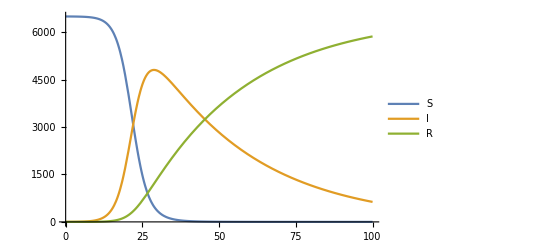

```mathematica
sols = {Total[s[t]],Total[i[t]],Total[r[t]]}/.sol//Flatten;
Plot[sols, {t,t1,t2},
PlotLegends->{"S", "I", "R"}]
```